```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/流体力学会2023/Ren2015_H0d04_T1d2_potential_2/result.json"*)

ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
ExperimentData0d04=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json"
name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2/result.json"
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_negative_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_potential_2/result.json"*)
```

/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json

/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2/result.json

/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json

```mathematica
imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
```

```mathematica
titles=imported[[;;,1]];
Column[titles,Background->{{LightGreen,Green}},Frame->True]
```

cpu_time
float_COM
float_EK
float_EP
float_accel
float_area
float_force
float_pitch
float_roll
float_torque
float_velocity
float_yaw
simulation_time
wall_clock_time
water_E
water_EK
water_EP
water_volume

```mathematica
Manipulate[
ListPlot[
{{getData["float_COM",1]-shift,getData["float_COM",3]-0.4}ᵀ
(*,{#1,#2}&@@@ExperimentData,*)
,{#1,#2}&@@@ExperimentData0d04},
PlotRange->All,
Joined->{False,True},
PlotStyle->{{Blue,Dashed},{Red}},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
(*AspectRatio->1/2,*)
(*GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},*)
Frame->True,
FrameLabel->{
Style["x",FontSize->20,FontFamily->"Times",Italic],
Style["y",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
],{shift,4.62,4.7}]
```

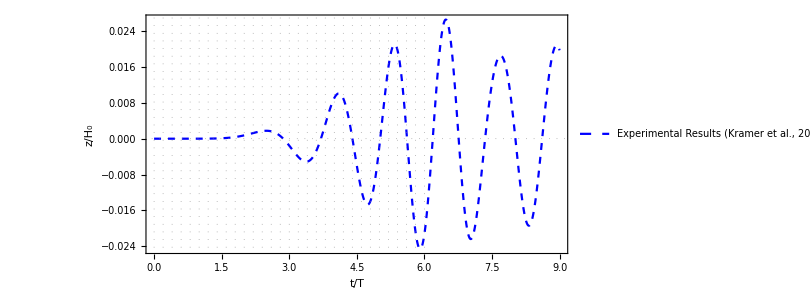

```mathematica
fig=ListPlot[
{getData["simulation_time"],getData["float_COM",3]-0.4}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

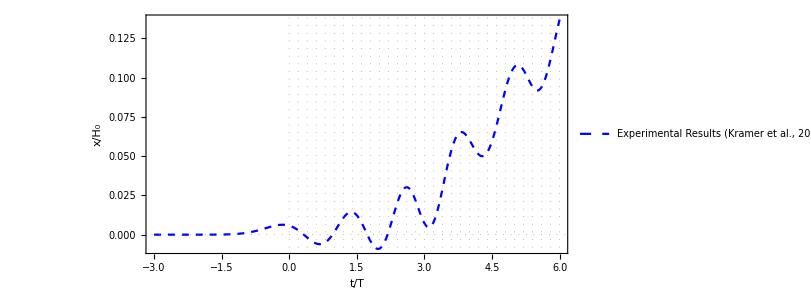

```mathematica
ListPlot[
{getData["simulation_time"]-3,getData["float_COM",1]-4.6}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

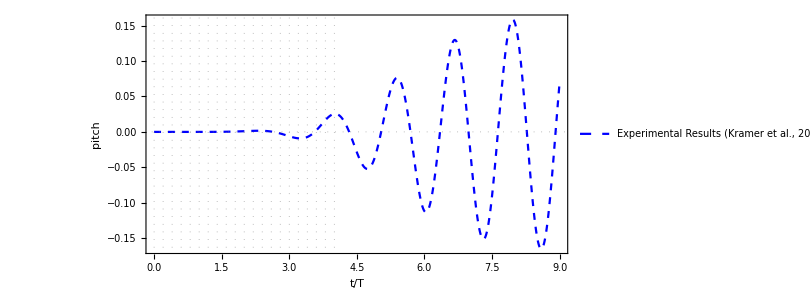

```mathematica
ListPlot[
{getData["simulation_time"],getData["float_pitch"]}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```